```mathematica
Clear[b]
Clear[c]
dataGoelOkumoto={{1,27},{2,43},{3,54},{4,64},{5,75},{6,82},{7,84},{8,89},{9,92},{10,93},{11,97},{12,104},{13,106},{14,111},{15,116},{16,122},{17,122},{18,127},{19,128},{20,129},{21,131},{22,132},{23,134},{24,135},{25,136}}

model=n*(1- Exp[-b*t^c]); (* n - предполагаемото число *)
fit=FindFit[data2,model,{b,c},t]
```

```mathematica
eval = Evaluate[model/.fit];
```

```mathematica
modelf=Function[{t},eval];
```

```mathematica
epilog = Epilog->Map[Point,data2];
```

```mathematica
plotRange = PlotRange->{0,160};
```

```mathematica
axesOrigin = AxesOrigin->{0,0};
```

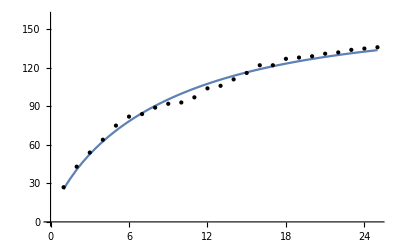

```mathematica
Plot[modelf[t],{t,1,25},Evaluate[epilog],Evaluate[plotRange],Evaluate[axesOrigin]]
```